```mathematica
#2 Cellular Automata- From Classical Computation to Quantum Error Correction #2
```

```mathematica
ClearAll["Global`*"];
CreateHistory[seed_,max_:150]:=Module[{frames={seed},hashes={Hash[seed]},game=CellularAutomaton["GameOfLife"],nxt,nxtHash},While[Length[frames]<max,nxt=game[Last[frames]];nxtHash=Hash[nxt];If[MemberQ[hashes,nxtHash],Break[]];AppendTo[frames,nxt];AppendTo[hashes,nxtHash]];frames]
OverlayFracs[base_,mask_,f_]:=MapThread[If[#2==1,f,#1]&,{base,mask},2]
MakeGrays[hist_]:=Module[{acc=ConstantArray[0.,{16,16}],n=Length[hist]},Do[acc=OverlayFracs[acc,hist⟦i⟧,i/n],{i,n}];acc]
NextInt[bits_,n_]:={FromDigits[Take[bits,n],2],Drop[bits,n]};
NextReal[bits_,n_]:=Module[{v,r},{v,r}=NextInt[bits,n];{N[v/(2^n-1)],r}];
NextFrac[bits_]:=NextReal[bits,16];
NextBool[bits_]:={First[bits]===1,Rest[bits]};
spectrumColors=RGBColor@@@N[1/255 {{0,168,222},{51,51,145},{233,19,136},{235,45,46},{253,233,43},{0,158,84},{0,168,222}}];
SpectrumColor[f_]:=Blend[spectrumColors,f]
Luminance[c_RGBColor]:=0.2126 c⟦1⟧+0.7152 c⟦2⟧+0.0722 c⟦3⟧
MonochromeGradient[hue_,tint_,rev_,kA_,nA_]:=Module[{key,neut,order},key=ColorConvert[Hue[hue,1,1],"RGB"];neut=ColorConvert[Hue[0,0,If[tint,1,0]],"RGB"];If[tint,key=Darker[key,.5]];order=If[rev,Reverse,Identity];With[{k=kA 0.3+.05,n=nA 0.3+.05},Blend[order[{Blend[{key,neut},k],Blend[{neut,key},n]}],#1]&]]
ComplementaryGradient[s_,lA_,dA_,rev_]:=Module[{cs,order},cs=SortBy[SpectrumColor/@{s,Mod[s+.5,1]},Luminance];order=If[rev,Reverse,Identity];With[{l=lA 0.3,d=dA 0.3},Blend[order[{Blend[{cs⟦1⟧,Black},d],Blend[{cs⟦2⟧,White},l]}],#1]&]]
TriadicGradient[s_,lA_,dA_,rev_]:=Module[{cs=SpectrumColor/@Mod[s+{0,1/3,2/3},1],order},cs=SortBy[cs,Luminance];order=If[rev,Reverse,Identity];With[{l=lA 0.3,d=dA 0.3},Blend[order[{Blend[{cs⟦1⟧,Black},d],cs⟦2⟧,Blend[{cs⟦3⟧,White},l]}],#1]&]]
AnalogousGradient[s_,adv_,rev_]:=Module[{cs=SpectrumColor/@Mod[s+1/12 Range[0,3],1],order},If[Luminance[First[cs]]>Luminance[Last[cs]],cs=Reverse[cs]];order=If[rev,Reverse,Identity];With[{a=adv .5+.2},Blend[order[{Blend[{cs⟦1⟧,Black},a],Blend[{cs⟦2⟧,Black},a/2],Blend[{cs⟦3⟧,White},a/2],Blend[{cs⟦4⟧,White},a]}],#1]&]]
SelectMonochrome[bits_]:=Module[{e=bits,h,t,r,kA,nA},{h,e}=NextFrac[e];{t,e}=NextBool[e];{r,e}=NextBool[e];{kA,e}=NextFrac[e];{nA,e}=NextFrac[e];{MonochromeGradient[h,t,r,kA,nA],e}]
SelectComplementary[bits_]:=Module[{e=bits,s,lA,dA,r},{s,e}=NextFrac[e];{lA,e}=NextFrac[e];{dA,e}=NextFrac[e];{r,e}=NextBool[e];{ComplementaryGradient[s,lA,dA,r],e}]
SelectTriadic[bits_]:=Module[{e=bits,s,lA,dA,r},{s,e}=NextFrac[e];{lA,e}=NextFrac[e];{dA,e}=NextFrac[e];{r,e}=NextBool[e];{TriadicGradient[s,lA,dA,r],e}]
SelectAnalogous[bits_]:=Module[{e=bits,s,adv,r},{s,e}=NextFrac[e];{adv,e}=NextFrac[e];{r,e}=NextBool[e];{AnalogousGradient[s,adv,r],e}]
SelectGradient[bits_]:=Module[{tag,rest,grad},{tag,rest}=NextInt[bits,2];{grad,rest}=Switch[tag,0,SelectMonochrome[rest],1,SelectComplementary[rest],2,SelectTriadic[rest],3,SelectAnalogous[rest]];{grad,rest}]
Transform[t_,rx_,ry_]:=Function[{x,y},With[{u=If[t,y,x],v=If[t,x,y]},{If[rx,33-u,u],If[ry,33-v,v]}]]
snowflake=Transform@@@{{False,False,False},{False,True,False},{False,False,True},{False,True,True}};
pinwheel=Transform@@@{{False,False,False},{True,True,False},{True,False,True},{False,True,True}};
SelectSymmetry[bits_]:=Module[{b,rest},{b,rest}=NextBool[bits];{If[b,"snowflake","pinwheel"],rest}]
ApplySymmetry[img_,pat_]:=Module[{tors=If[pat==="snowflake",snowflake,pinwheel]},ReplacePart[ConstantArray[0.,{32,32}],Flatten[Table[(#1@@{x,y}->img⟦y,x⟧&)/@tors,{y,16},{x,16}]]]]
Fingerprint[val_]:=Module[{bits=IntegerDigits[Hash[val,"SHA256"],2,256],seed,hist,gray,grad,restBits,pat},seed=Partition[bits,16];hist=CreateHistory[seed];gray=MakeGrays[hist];{grad,restBits}=SelectGradient[bits];{pat,restBits}=SelectSymmetry[restBits];{ApplySymmetry[gray,pat],grad}]
Options[LifeHash]={ImageSize->512};
LifeHash[value_,opts:OptionsPattern[]]:=Module[{img,cf},{img,cf}=Fingerprint[value];ArrayPlot[img,ColorFunction->cf,Frame->False,PixelConstrained->1,ImageSize->OptionValue[ImageSize]]]
LifeHash["Wolf"]
LifeHash["Daedalus"]
LifeHash[Range[20]]
```

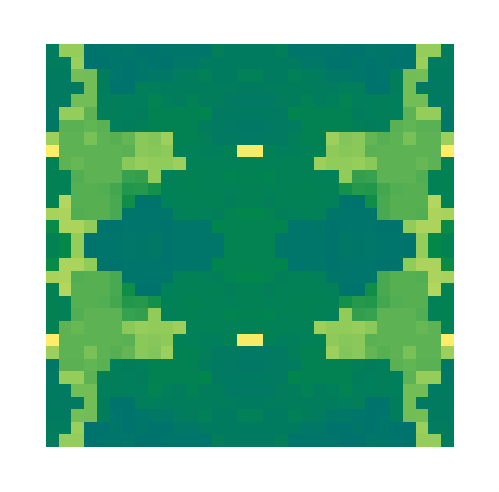

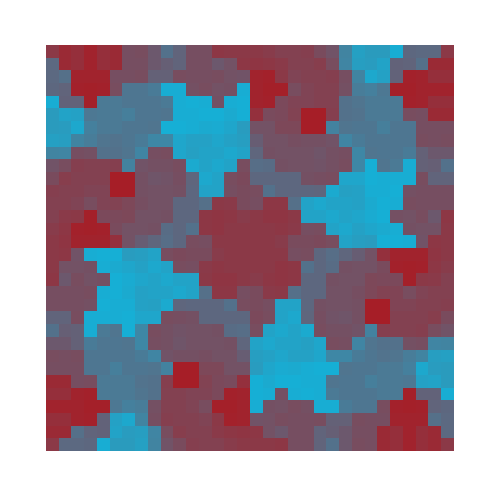

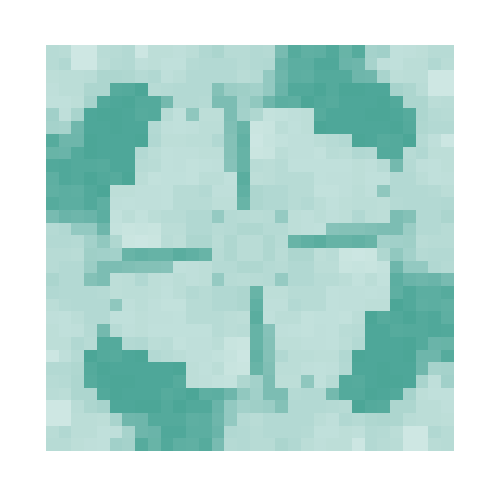

This project reinterprets Conway Game of Life (GPU-only) not as a mere visualization tool, but as a “code-as-proof” model for creating a deterministic, self-organizing representation from a causal seed, mirroring the core tenets of the Daedaelus philosophy. Here, the cryptographic hash of an input serves as the initial, conserved quantity of information. This seed is not broadcast to a global controller; instead, it provides the local rules for a computational fabric—a cellular automaton—that evolves based on “local information only,” creating a complex and unique structural history without a God’s-Eye-View. This emergent structure can be seen as the “groundplane.” The Graph Virtual Machine (GVM) then applies a deterministic policy, also derived from the initial seed, to this groundplane, selecting the symmetry and coloring rules that create the final, coherent form. The resulting icon is therefore not just a picture, but a verifiable, information-rich artifact representing the complete, self-contained evolution of its initial state, much like how the Transaction Fabric aims to make all operations within it transparent and provably correct.

Finite Element Mesh:

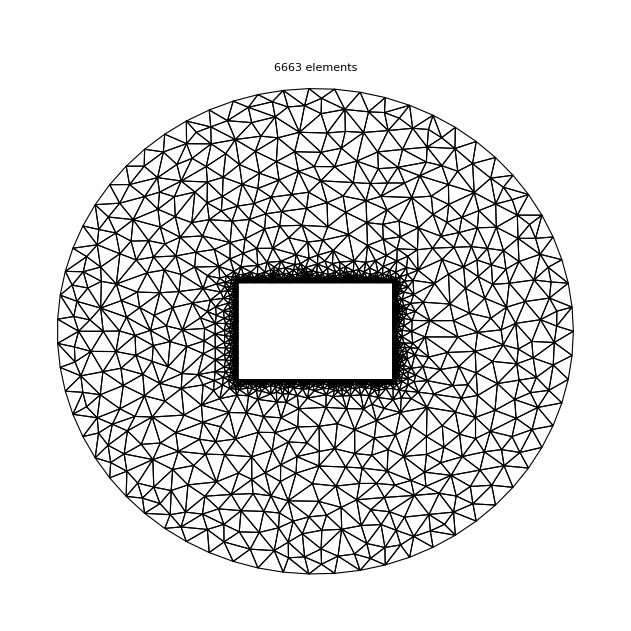

3D Plot of Solution:

-Graphics3D-

Coating Profile Comparison (Ideal vs. Actual):

-Graphics-

```mathematica
BeginPackage["Conway`"];
Unprotect["Conway`*"];
ClearAll["Conway`*"];
ClearAll["Conway`*`*"];
{BasicImageResolution,BoxedLabel,ContourByArcLength,CurveLegend,DecimalPlacesForm,DefaultColours,DeleteNearbyPoints,DomainEnd,DomainStart,Embolden,EmptyAxes,EmptyFrame,EvaluatePair,Ex,ExportIfNotExists,FString,ImageSizeCentimetre,IncludeYReflection,Italicise,LatinModernFont,LatinModernLabelStyle,LatinModernFontStyle,LaTeXStyle,Margined,ModuleSymbol,NodeLegend,NoExtrapolation,OffsetCharacterCode,OnePointPerspective,ParametricTangent,PlotOptions,PreciseOptions,PrettyString,RegionLegend,ReInterpolate,SeekFirstRootBisection,SeekParametricIntersection,SeekRoot,SeekRootBisection,SeparatedRow,SignificantFiguresForm,SortByPhi,ToName,UniformRange,Way};
Begin["`Private`"];
BasicImageResolution::usage = ("BasicImageResolution\n" <> "Returns frugal ImageResolution of 72.");
BasicImageResolution = 72;
BoxedLabel::usage = ("BoxedLabel[expr, opts]\n" <> "Returns framed version of the expression expr.\n" <> "To be used for PlotLabel.");
BoxedLabel[expr_, opts : OptionsPattern[Framed]] := Framed[expr, ImageMargins -> {{0, 0}, {10, 0}}, opts];
ContourByArcLength::usage = ("ContourByArcLength[fun][{x0, y0}, s0, {sStart, sEnd}\n" <> "  , sSign (def 1)\n" <> "  , terminationFunction (def False &)\n" <> "]\n" <> "Returns contour x == x(s), y == y(s) " <> "(arc-length parametrisation) for:\n" <> "- Function fun == fun(x, y)\n" <> "- Initial condition x(s0) == x0, y(s0) == y0\n" <> "- Arc-length interval sStart < s < sEnd.\n" <> "To traverse the contour backwards, use sSign == -1.\n");
ContourByArcLength[fun_][{x0_, y0_}, s0_, {sStart_, sEnd_}, sSign_: 1, terminationFunction_: (False &)] := Module[{p, q, grad, xDerivative, yDerivative, dummyForTrailingCommas}, p = Derivative[1, 0][fun]; q = Derivative[0, 1][fun]; grad = Function[{x, y}, Sqrt[p[x, y]^2 + q[x, y]^2] // Evaluate]; xDerivative[x_, y_] := +q[x, y]/grad[x, y]; yDerivative[x_, y_] := -p[x, y]/grad[x, y]; With[{x = x, y = y, s = s}, NDSolveValue[{x'[s] == sSign xDerivative[x[s], y[s]], y'[s] == sSign yDerivative[x[s], y[s]], x[s0] == x0, y[s0] == y0, WhenEvent[terminationFunction[x[s], y[s]], "StopIntegration"]}, {x, y}, {s, sStart, sEnd}, NoExtrapolation]]];
CurveLegend::usage = ("CurveLegend[styleList, labelList, opts]\n" <> "Returns list of individual LineLegends for each {style, label} pair. " <> "To be used in Grid.");
CurveLegend[styleList_List, labelList_List, opts : OptionsPattern[LineLegend]] := Module[{nMax, style, label}, nMax = Length /@ {styleList, labelList} // Min; Table[style = styleList[[n]]; label = labelList[[n]]; LineLegend[{style}, {label}, opts, LegendMarkerSize -> {25, 16}], {n, nMax}]];
DecimalPlacesForm::usage = ("DecimalPlacesForm[n][x]\n" <> "Return x formatted to n decimal places.");
DecimalPlacesForm[n_Integer][x_] := DecimalForm[N[x], {Infinity, n}];
DefaultColours::usage = ("DefaultColours\n" <> "Returns the default colours for Plot since Version 10.");
DefaultColours = ColorData[97, "ColorList"];
DeleteNearbyPoints::usage = ("DeleteNearbyPoints[sep][list]\n" <> "Removes duplicates from the list of points list, " <> "where points with separation less than sep are considered duplicate.");
DeleteNearbyPoints[sep_?NumericQ][list_List] := DeleteDuplicates[list, Norm[#2 - #1] < sep &];
DomainEnd::usage = ("DomainEnd[iFun] or DomainEnd[{iFun, ...}]\n" <> "Returns the end of the domain for the first coordinate " <> "of the interpolating function iFun.");
DomainEnd[iFun_InterpolatingFunction] := iFun["Domain"][[1, 2]];
DomainEnd[{iFun_, ___}] := DomainEnd[iFun];
DomainStart::usage = ("DomainStart[iFun] or DomainStart[{iFun, ...}]\n" <> "Returns the start of the domain for the first coordinate " <> "of the interpolating function iFun.");
DomainStart[iFun_InterpolatingFunction] := iFun["Domain"][[1, 1]];
DomainStart[{iFun_, ___}] := DomainStart[iFun];
Embolden::usage = ("Embolden[str]\n" <> "Returns emboldened version of str." <> "Automatically threads over lists.");
Embolden[str_] := Style[str, Bold];
SetAttributes[Embolden, Listable];
EmptyAxes::usage = ("EmptyAxes[{xMin, xMax}, {yMin, yMax}, opts]\n" <> "Returns empty Plot with default options PlotOptions[Axes], " <> "which may be overridden by options opts.");
EmptyAxes[{xMin_?NumericQ, xMax_?NumericQ}, {yMin_?NumericQ, yMax_?NumericQ}, opts : OptionsPattern[Plot]] := Plot[Indeterminate, {x, xMin, xMax}, opts, PlotRange -> {{xMin, xMax}, {yMin, yMax}}, PlotOptions[Axes] // Evaluate];
EmptyFrame::usage = ("EmptyFrame[{xMin, xMax}, {yMin, yMax}, opts]\n" <> "Returns empty RegionPlot with default options PlotOptions[Frame], " <> "which may be overridden by options opts.");
EmptyFrame[{xMin_?NumericQ, xMax_?NumericQ}, {yMin_?NumericQ, yMax_?NumericQ}, opts : OptionsPattern[RegionPlot]] := RegionPlot[False, {x, xMin, xMax}, {y, yMin, yMax}, opts, PlotOptions[Frame] // Evaluate];
EvaluatePair::usage = ("EvaluatePair[{xFun, yFun}, s, ySign (def 1)]\n" <> "Returns {xFun[s], yFun[s] * ySign}.");
EvaluatePair[{xFun_, yFun_}, s_, ySign_: 1] := {xFun[s], yFun[s]*ySign};
Ex::usage = ("Ex[dest, opts]\n" <> "Operator form of Export. Now modified to display graphic in notebook instead.");
Ex[dest_, opts : OptionsPattern[Export]] := Identity[#] &;
ExportIfNotExists::usage = ("ExportIfNotExists[dest, expr, opts]\n" <> "This function is now obsolete. The notebook uses memoization instead of file-based caching.");
ExportIfNotExists[dest_, expr_, opts : OptionsPattern[Export]] := If[Not@FileExistsQ[dest], expr // Ex[dest, opts]];
SetAttributes[ExportIfNotExists, HoldAll];
FString::usage = ("FString[s]\n" <> "Formats string s as per Python 3.6's f-strings: " <> "contents of curly brackets are evaluated using ToExpression " <> "(use doubled curly brackets for literal brackets).\n" <> "Referencing With variables will NOT work.\n" <> "Avoid referencing free variables: this will be SLOW.\n" <> "Automatically threads over lists.\n" <> "See PEP 498 -- Literal String Interpolation: " <> "https://www.python.org/dev/peps/pep-0498/");
FString[s_String] := s // StringReplace@{"{{" -> "{", "}}" -> "}", StringExpression["{", contents:Shortest[___], "}"] :> ToString[ToExpression[contents] // ReplaceAll[x_Symbol :> ModuleSymbol[SymbolName[x], $ModuleNumber]] // ReplaceRepeated[#, x_Symbol :> ModuleSymbol[SymbolName[x] // StringReplace["$" ~~ __ -> ""], SymbolName[x] // StringReplace[__ ~~ "$" -> ""] // ToExpression // Max[1, # - 1] &], MaxIterations -> Infinity] & // ReplaceAll[x_Symbol :> Symbol[SymbolName[x] // StringReplace["$" ~~ __ -> ""]]]]};
SetAttributes[FString, Listable];
ImageSizeCentimetre::usage = ("ImageSizeCentimetre\n" <> "Returns number of printer's points in 1 centimetre.\n" <> "To be used for raster exports.");
ImageSizeCentimetre = Module[{inchDividedByPoint, inchDividedByCentimetre}, inchDividedByPoint = 72; inchDividedByCentimetre = 254/100; inchDividedByPoint/inchDividedByCentimetre];
IncludeYReflection::usage = ("IncludeYReflection[{x, y}]\n" <> "Returns {{x, y}, {x, -y}}.");
IncludeYReflection[{x_, y_}] := {{x, y}, {x, -y}};
Italicise::usage = ("Italicise[str]\n" <> "Returns italicised version of str.\n" <> "To be used for AxesLabel etc.\n" <> "Automatically threads over lists.");
Italicise[str_] := Style[str, Italic];
SetAttributes[Italicise, Listable];
LatinModernFont::usage = ("LatinModernFont[type (def \"Roman\")]\n" <> "Latin Modern Font of type type.\n" <> "Requires installation of the following fonts:\n" <> "* \"Latin Modern Math\" latinmodern-math.otf\n" <> "  <http://www.gust.org.pl/projects/e-foundry/lm-math/download>" <> "\n" <> "* \"LM Roman 10\" lmroman10-regular.otf\n" <> "  <http://www.gust.org.pl/projects/e-foundry/latin-modern/download>");
LatinModernFont[type : _String : "Roman"] := Association["Math" -> "Latin Modern Math", "Roman" -> "LM Roman 10"][type];
LatinModernLabelStyle::usage = ("LatinModernLabelStyle[size, col (def Black)]\n" <> "Latin Modern Font label style to be used in Plots etc.");
LatinModernLabelStyle[size_Integer, col_: Black] := {col, FontFamily -> LatinModernFont[], FontSize -> size};
LatinModernFontStyle::usage = ("LatinModernFontStyle[type][expr]\n" <> "Style expression expr with Latin Modern Font of type type.");
LatinModernFontStyle[type_][expr_] := Style[expr, FontFamily -> LatinModernFont[type]];
LaTeXStyle::usage = ("LaTeXStyle[expr]\n" <> "Style expression expr with LaTeX fonts without using Szabolcs's MaTeX. " <> "While MaTeX is an excellent package, and outputs vector text labels, " <> "those labels cannot be selected and copied.\n" <> "Requires installation of the following fonts:\n" <> "* \"Latin Modern Math\" latinmodern-math.otf\n" <> "  <http://www.gust.org.pl/projects/e-foundry/lm-math/download>" <> "\n" <> "* \"LM Roman 10\" lmroman10-regular.otf\n" <> "  <http://www.gust.org.pl/projects/e-foundry/latin-modern/download>");
LaTeXStyle[expr_] := (LatinModernFontStyle["Roman"][expr] /. {{"d", x_} :> (SeparatedRow["NegativeVeryThin"]["d", x]), {"∂", x_} :> (SeparatedRow[][ToString["∂"], x])} /. {char_String?((StringMatchQ[#1, CharacterRange["α", "ω"]]) & ) :> (char // OffsetCharacterCode["α", 16^^1D6FC] // LatinModernFontStyle["Math"]), char_String?((StringMatchQ[#1, CharacterRange["Α", "Ω"]]) & ) :> (char // OffsetCharacterCode["Α", 16^^0391] // LatinModernFontStyle["Math"]), "∂" :> (FromCharacterCode[16^^1D715] // LatinModernFontStyle["Math"]), "ϵ" :> (FromCharacterCode[16^^1D716] // LatinModernFontStyle["Math"]), "ϑ" :> (FromCharacterCode[16^^1D717] // LatinModernFontStyle["Math"]), "ϰ" :> (FromCharacterCode[16^^1D718] // LatinModernFontStyle["Math"]), "ϕ" :> (FromCharacterCode[16^^1D719] // LatinModernFontStyle["Math"]), "ϱ" :> (FromCharacterCode[16^^1D71A] // LatinModernFontStyle["Math"]), "ϖ" :> (FromCharacterCode[16^^1D71B] // LatinModernFontStyle["Math"])});
Margined::usage = ("Margined[margins, opts]\n" <> "Operator form of Framed, equivalent to " <> "Framed[#, opts, FrameMargins -> margins, FrameStyle -> None] &");
Margined[margins_, opts : OptionsPattern[Framed]] := Framed[#1, opts, FrameMargins -> margins, FrameStyle -> None] & ;
ModuleSymbol::usage = ("ModuleSymbol[name, num]\n" <> "Builds the symbol with name name and $ModuleNumber num.");
ModuleSymbol[name_String, num_Integer] := Symbol@StringJoin[name, "$", ToString[num]];
NodeLegend::usage = ("NodeLegend[styleList, labelList, opts]\n" <> "Returns list of individual PointLegends for each {style, label} pair. " <> "To be used in Grid.");
NodeLegend[styleList_List, labelList_List, opts : OptionsPattern[PointLegend]] := Module[{nMax, style, label}, nMax = Length /@ {styleList, labelList} // Min; Table[style = styleList[[n]]; label = labelList[[n]]; PointLegend[{style}, {label}, opts], {n, nMax}]];
NoExtrapolation::usage = ("NoExtrapolation\n" <> "Undocumented option for preventing extrapolation " <> "in InterpolatingFunction etc.");
NoExtrapolation = ("ExtrapolationHandler" -> {Indeterminate &, "WarningMessage" -> False});
OffsetCharacterCode::usage = ("OffsetCharacterCode[offset][string]\n" <> "Offset code points of string by an integer offset.\n" <> "OffsetCharacterCode[initial, final][string]\n" <> "Offset code points of string from initial to final. " <> "Both initial and final may be given " <> "as integers (code points) or as strings (first characters).");
OffsetCharacterCode[offset_Integer][string_String] := FromCharacterCode[ToCharacterCode[string] + offset];
OffsetCharacterCode[initial_Integer, final_Integer] := OffsetCharacterCode[final - initial];
OffsetCharacterCode["", final_] := OffsetCharacterCode[0, final];
OffsetCharacterCode[initial_String, final_] := OffsetCharacterCode[First@ToCharacterCode[initial], final];
OffsetCharacterCode[initial_, ""] := OffsetCharacterCode[initial, 0];
OffsetCharacterCode[initial_, final_String] := OffsetCharacterCode[initial, First@ToCharacterCode[final]];
OnePointPerspective::usage = ("OnePointPerspective[d][e, n, r0, v][p]\n" <> "Returns d-dimensional coordinates for one-point perspective for:\n" <> "- Dimension d == 2 (canvas components) or d == 3 (spatial coordinates)\n" <> "- Eye at e in 3D\n" <> "- Canvas plane in 3D with normal n containing point r0\n" <> "- Vertical axis v in 3D\n" <> "- Point p in 3D\n" <> "There are far better ways than the simple implementation here, " <> "but I am not a 3D graphics expert.");
OnePointPerspective[d : 2 | 3][e_, n_, r0_, v_][p_] := Module[{rFunction, r, b, a, x, y}, rFunction[point_] := e + n.(r0 - e)/n.(point - e)*(point - e); r = rFunction[p]; b = rFunction[v] - rFunction[0]; a = Cross[b, Normalize[n]]; x = r.a/a.a; y = r.b/b.b; If[d == 2, {x, y}, r]];
ParametricTangent::usage = ("ParametricTangent[{x, y, ...}, s]\n" <> "Returns (un-normalised) tangent vector of {x, y, ...} evaluated at s." <> "To be used for rotation of Text labelling a parametric curve.");
ParametricTangent[funList_List, s_] := Table[fun'[s], {fun, funList}];
PlotOptions::usage = ("PlotOptions[type]\n" <> "Returns sensible options for a plot of type type, " <> "either Axes or Frame.");
PlotOptions[Axes] = {AxesLabel -> Italicise@{"x", "y"}, LabelStyle -> Directive[Black, 16]};
PlotOptions[Frame] = {AspectRatio -> Automatic, FrameLabel -> Italicise@{"x", "y"}, LabelStyle -> Directive[Black, 16], RotateLabel -> False};
PreciseOptions::usage = ("Precise[maxStepFrac (def 1/512)]\n" <> "Returns options for high precision in NDSolve.\n" <> "These may be overridden by options called before PreciseOptions.");
PreciseOptions[maxStepFrac : _?NumericQ : 1/512] := {MaxStepFraction -> maxStepFrac, MaxSteps -> Infinity, AccuracyGoal -> 16, PrecisionGoal -> 16, WorkingPrecision -> 2 MachinePrecision};
PrettyString::usage = ("PrettyString[s1 -> sp1, s2 -> sp2, ...][expr]\n" <> "Performs string replacements {s1 -> sp1, s2 -> sp2, ...} " <> "on all string subparts of expr.\n" <> "To be used to make pretty output with readable input.");
PrettyString[ruleSeq___Rule][expr_] := expr /. s_String :> StringReplace[s, {ruleSeq}];
RegionLegend::usage = ("RegionLegend[styleList, labelList, opts]\n" <> "Returns list of individual SwatchLegends for each {style, label} pair. " <> "To be used in Grid.");
RegionLegend[styleList_List, labelList_List, opts : OptionsPattern[SwatchLegend]] := Module[{nMax, style, label}, nMax = Length /@ {styleList, labelList} // Min; Table[style = styleList[[n]]; label = labelList[[n]]; SwatchLegend[{style}, {label}, opts, LegendMarkerSize -> 12], {n, nMax}]];
ReInterpolate::usage = ("ReInterpolate[iFun, num (def 1024)]\n" <> "Re-interpolates interpolating function iFun using num uniform subintervals " <> "if iFun has more than num subintervals.\n" <> "To be used to save space.\n" <> "Automatically threads over lists.");
ReInterpolate[iFun_InterpolatingFunction, num : _?NumericQ : 1024] := If[Length@iFun["Grid"] - 1 > num, Interpolation@Table[{x, iFun[x]}, {x, Subdivide[DomainStart[iFun], DomainEnd[iFun], num]}], iFun];
SetAttributes[ReInterpolate, Listable];
SeekFirstRootBisection::usage = ("SeekFirstRootBisection[fun, {xMin, xMax}, num (def 1000), tol (def 10^-6), " <> "opts (def N -> True, \"ReturnIterations\" -> False, " <> "\"ToleranceType\" -> \"Absolute\")]\n" <> "Seeks a numerical root of fun[x] == 0, using the bisection algorithm " <> "over the subinterval {x0, x1} corresponding to the first sign-change " <> "as determined by num subdivisions of the interval {xMin, xMax}, " <> "with tolerance tol over {x0, x1}.\n" <> "Default option N -> True specifies that initial endpoints " <> "should be numericised (for speed) before performing the iteration.\n" <> "Default option \"ReturnIterations\" -> \"False\" " <> "specifies that the number of iterations should not be returned.\n" <> "Default option \"ToleranceType\" -> \"Absolute\" " <> "specifies absolute tolerance. " <> "Use \"ToleranceType\" -> \"Relative\" " <> "for tolerance relative to the interval {x0, x1}.");
SeekFirstRootBisection[fun_, {xMin_?NumericQ, xMax_?NumericQ}, num : Except[_?OptionQ, _?NumericQ] : 1000, tol : Except[_?OptionQ, _?NumericQ] : 10^-6, opts : OptionsPattern@{N -> True, "ReturnIterations" -> False, "ToleranceType" -> "Absolute"}] := Module[{xValues, firstSignChangeIndex, x0, x1}, xValues = (Subdivide[xMin, xMax, num] // If[TrueQ@OptionValue[N], N, Identity]); firstSignChangeIndex = (First@FirstPosition[Differences@Sign[fun /@ xValues], signChange_ /; signChange != 0]); x0 = xValues[[firstSignChangeIndex]]; x1 = xValues[[firstSignChangeIndex + 1]]; SeekRootBisection[fun, {x0, x1}, tol, # -> OptionValue[#] & /@ {N, "ReturnIterations", "ToleranceType"}]];
SeekParametricIntersection::usage = ("SeekParametricIntersection[" <> "{x1, y1}, {x2, y2}, " <> "{start1, end1}, {start2, end2}, " <> "prop1 (def 1/2), prop2 (def 1/2)]\n" <> "Seeks intersection of the parametric curves " <> "(x1, y1)(t1) and (x2, y2)(t2) " <> "over the domains start1 < t1 < end1, start2 < t2 < end2 respectively " <> "with initial guess at proportions prop1 and prop2 of the way respectively. " <> "If both x1 and x2 are interpolating functions, " <> "{start1, end1} and {start2, end2} are chosen automatically if omitted.");
SeekParametricIntersection[{x1_, y1_}, {x2_, y2_}, {start1_, end1_}, {start2_, end2_}, prop1_ : 1/2, prop2_ : 1/2] := Module[{t1Init, t2Init}, t1Init = Way[start1, end1, prop1]; t2Init = Way[start2, end2, prop2]; FindRoot[{x1[#1] - x2[#2], y1[#1] - y2[#2]} &, {{t1Init}, {t2Init}}]];
SeekParametricIntersection[{x1_InterpolatingFunction, y1_}, {x2_InterpolatingFunction, y2_}, prop1_ : 1/2, prop2_ : 1/2] := SeekParametricIntersection[{x1, y1}, {x2, y2}, {DomainStart[x1], DomainEnd[x1]}, {DomainStart[x2], DomainEnd[x2]}, prop1, prop2];
SeekRoot::usage = ("SeekRoot[fun, {xMin, xMax}, num (def 1000), opts (def N -> True)]\n" <> "Seeks a numerical root of fun[x] == 0, using FindRoot, " <> "over the search interval {xMin, xMax} " <> "with num initial subdivisions to determine the best initial guess.\n" <> "Default option N -> True specifies that initial subdivision points " <> "should be numericised (for speed) before fun is applied.\n\n" <> "SeekRoot[fun, xInit]\n" <> "Uses initial guess xInit.");
SeekRoot[fun_, {xMin_?NumericQ, xMax_?NumericQ}, num : Except[_?OptionQ, _?NumericQ] : 1000, opts : OptionsPattern@{N -> True}] := Module[{xInit}, xInit = First@TakeSmallestBy[Subdivide[xMin, xMax, num] // If[TrueQ@OptionValue[N], N, Identity], Abs@*fun, 1, ExcludedForms -> Except[_?NumericQ]]; First@FindRoot[fun, {xInit}]];
SeekRoot[fun_, xInit_?NumericQ] := First@FindRoot[fun, {xInit}];
SeekRootBisection::usage = ("SeekRootBisection[fun, {xMin, xMax}, tol (def 10^-6), " <> "opts (def N -> True, \"ReturnIterations\" -> False, " <> "\"ToleranceType\" -> \"Absolute\")]\n" <> "Seeks a numerical root of fun[x] == 0, using the bisection algorithm, " <> "over the search interval {xMin, xMax} with tolerance tol.\n" <> "Default option N -> True specifies that initial endpoints " <> "should be numericised (for speed) before performing the iteration.\n" <> "Default option \"ReturnIterations\" -> \"False\" " <> "specifies that the number of iterations should not be returned.\n" <> "Default option \"ToleranceType\" -> \"Absolute\" " <> "specifies absolute tolerance. " <> "Use \"ToleranceType\" -> \"Relative\" " <> "for tolerance relative to the interval {xMin, xMax}.");
SeekRootBisection[fun_, {xMin_?NumericQ, xMax_?NumericQ}, tol : Except[_?OptionQ, _?NumericQ] : 10^-6, opts : OptionsPattern@{N -> True, "ReturnIterations" -> False, "ToleranceType" -> "Absolute"}] := Module[{absTol, num, xLeft, xRight, xMid, xSol}, absTol = tol; If[OptionValue["ToleranceType"] =!= "Absolute", absTol *= xMax - xMin]; num = 1; {xLeft, xRight} = (MinMax@{xMin, xMax} // If[TrueQ@OptionValue[N], N, Identity]); While[num < $RecursionLimit, xMid = Way[xLeft, xRight]; If[(xRight - xLeft)/2 < absTol, xSol = xMid; Break[]]; If[fun[xLeft] fun[xMid] > 0, xLeft = xMid, xRight = xMid]; num += 1]; If[TrueQ@Not@OptionValue["ReturnIterations"], xSol, {xSol, num}]];
SeparatedRow::usage = ("SeparatedRow[sep (def \"\")][x1, ...]\n" <> "Returns Row for list {x1, ...} and separator sep.\n" <> "Abbreviations for certain horizontal spacing characters " <> "are defined for sep.");
SeparatedRow[sep_: ""][xSeq___] := Row[{xSeq}, sep /. {"VeryThin" -> "", "Thin" -> " ", "Medium" -> " ", "Thick" -> " ", "Invisible" -> "", "NegativeVeryThin" -> "", "NegativeThin" -> "", "NegativeMedium" -> "", "NegativeThick" -> "", "NonBreaking" -> " ", Automatic -> ""}];
SignificantFiguresForm::usage = ("SignificantFiguresForm[n][x]\n" <> "Return x formatted to n significant figures.");
SignificantFiguresForm[n_Integer][x_] := Module[{pMin, pMax, digitsSpec}, {pMin, pMax} = ScientificNotationThreshold /. Options[NumberForm]; digitsSpec = If[10^pMin <= Abs[x] < 10^pMax, {n, n - Floor[1 + Log10@Abs[x]]}, {n, n - 1}]; NumberForm[N[x], digitsSpec]];
SortByPhi::usage = ("SortByPhi[list]\n" <> "Sorts the list of (planar) points list by azimuthal angle.");
SortByPhi = SortBy[Mod[ArcTan @@ #, 2 Pi] &];
ToName::usage = ("ToName[number]\n" <> "Converts real number to a string for a file name, " <> "with decimal places replaced by underscores.");
ToName[number_Integer | number_Real] := StringReplace[ToString@DecimalForm[number], "." -> "_"];
ToName[number_?NumericQ] /; Im[number] == 0 := ToName[Re@number // N];
UniformRange::usage = ("UniformRange[start, end, maxStep]\n" <> "Subdivides the interval from start to end uniformly " <> "with step at most maxStep.");
UniformRange[start_?NumericQ, end_?NumericQ, maxStep_?NumericQ] := Subdivide[start, end, (end - start)/maxStep // N // Ceiling];
Way::usage = ("Way[start, end, prop (def 1/2)]\n" <> "Returns proportion prop of the way from start to end.\n" <> "The default for prop is 1/2 (halfway).");
Way[start_, end_, prop_ : 1/2] := (1 - prop) start + prop*end;
End[];
Protect["Conway`*"];
EndPackage[];
BeginPackage["FigureStyles`", {"Conway`"}];
Unprotect["FigureStyles`*"];
ClearAll["FigureStyles`*"];
ClearAll["FigureStyles`*`*"];
{GeneralStyle, BoundaryTracingStyle, ImageSizeTextWidth, ImageSizeTextWidthBeamer, LabelSize, SquigglyArrow, SlidesStyle, {}};
Begin["`Private`"];
GeneralStyle[type_String : Automatic] := Association["AmbientLighting" -> {{"Ambient"}, White}, "Dashed" -> AbsoluteDashing@{5, 4}, "DefaultThick" -> AbsoluteThickness[1.5], "Dotted" -> AbsoluteDashing@{0.3, 4}, "Point" -> PointSize[Large], "Thick" -> AbsoluteThickness[2.5], "Translucent" -> Opacity[0.7], "VeryThick" -> AbsoluteThickness[5], Automatic -> Automatic][type];
BoundaryTracingStyle[type : (_String | Automatic) : Automatic] := Association["Background" -> Directive[GeneralStyle["DefaultThick"], GrayLevel[0.7]], "Contour" -> Directive[GeneralStyle["DefaultThick"], GeneralStyle["Dotted"], Black], "ContourImportant" -> Directive[GeneralStyle["Thick"], Gray], "ContourPlain" -> Directive[GeneralStyle["DefaultThick"], GrayLevel[0.6]], "Edge3D" -> Thick, "NonViable" -> Directive[GeneralStyle["Translucent"], GrayLevel[0.8]], "Solution3D" -> White, "Terminal" -> Directive[GeneralStyle["DefaultThick"], GeneralStyle["Dashed"], Black], "Traced" -> Directive[GeneralStyle["Thick"], Black], "Unphysical" -> Black, "Viable" -> White, "Wall" -> Directive[GeneralStyle["DefaultThick"], Gray], "Wall3D" -> GrayLevel[0.6], Automatic -> Black][type];
BoundaryTracingStyle[typeSeq__String] := Directive @@ BoundaryTracingStyle /@ {typeSeq};
ImageSizeTextWidth = Module[{a4width, bindingoffset, inner, outer}, a4width = 21 Conway`ImageSizeCentimetre; bindingoffset = 2 Conway`ImageSizeCentimetre; inner = 2 Conway`ImageSizeCentimetre; outer = 2.5 Conway`ImageSizeCentimetre; a4width - (bindingoffset + inner + outer)];
ImageSizeTextWidthBeamer = 10.8 Conway`ImageSizeCentimetre;
LabelSize[type_String : Automatic] := Association["Axis" -> 12, "Label" -> 12, "LabelOmega" -> If[$OperatingSystem == "Windows", 13, 15], "Legend" -> 10, "Point" -> 11, "PointBracket" -> 15, "Straight" -> 10, "Tick" -> 9, Automatic -> Automatic][type];
SquigglyArrow[{xBase_, yBase_}, phi_: 0, size_: 1] := Module[{yList, listLength, xList, pointList}, yList = {ConstantArray[-0.1, 5], 1, 0, -1, 0, 1, 0, -1, ConstantArray[+0.1, 7], {}} // 0.15 # & // Flatten; listLength = Length[yList]; xList = Subdivide[0, 1, listLength - 1]; pointList = {xList, yList} // Transpose; Arrow@BSplineCurve[pointList // ScalingTransform@{size, size} // RotationTransform[phi, {0, 0}] // TranslationTransform@{xBase, yBase}]];
SlidesStyle[type_String : Automatic] := Association["Boundary" -> RGBColor["#9400D3"], "Interior" -> Blue, "InteriorRegion" -> RGBColor["#DEF0FF"], "Source" -> Red, "SourceRegion" -> RGBColor["#FFD9D9"], Automatic -> Automatic][type];
End[];
Protect["FigureStyles`*"];
EndPackage[];
BeginPackage["Curvilinear`"];
Unprotect["Curvilinear`*"];
ClearAll["Curvilinear`*"];
ClearAll["Curvilinear`*`*"];
{XBipolar, YBipolar, XYBipolar, UBipolar, VBipolar, UVBipolar, HBipolar, HUBipolar, HVBipolar, CBipolar, SBipolar, AUBipolar, AVBipolar};
{XPolar, YPolar, XYPolar, RPolar, PhiPolar, RPhiPolar, HRPolar, HPhiPolar, ARPolar, APhiPolar};
Begin["`Private`"];
XBipolar[u_, v_] := Sinh[v]/(Cosh[v] - Cos[u]);
YBipolar[u_, v_] := Sin[u]/(Cosh[v] - Cos[u]);
XYBipolar[u_, v_] := {XBipolar, YBipolar} @@ {u, v} // Through // Evaluate;
UBipolar[x_, y_] := ArcTan[x^2 + y^2 - 1, 2 y];
VBipolar[x_, y_] := ArcTanh[2 x/(x^2 + y^2 + 1)];
UVBipolar[x_, y_] := {UBipolar, VBipolar} @@ {x, y} // Through // Evaluate;
HBipolar[u_, v_] := 1/(Cosh[v] - Cos[u]);
HUBipolar[u_, v_] := HBipolar[u, v] // Evaluate;
HVBipolar[u_, v_] := HBipolar[u, v] // Evaluate;
CBipolar[u_, v_] := Cos[u] Cosh[v] - 1;
SBipolar[u_, v_] := Sin[u] Sinh[v];
AUBipolar[u_, v_] := HBipolar[u, v] {-SBipolar[u, v], CBipolar[u, v]} // Evaluate;
AVBipolar[u_, v_] := HBipolar[u, v] {-CBipolar[u, v], -SBipolar[u, v]} // Evaluate;
XPolar[r_, phi_] := r Cos[phi];
YPolar[r_, phi_] := r Sin[phi];
XYPolar[r_, phi_] := {XPolar, YPolar} @@ {r, phi} // Through // Evaluate;
RPolar[x_, y_] := Sqrt[x^2 + y^2];
PhiPolar[x_, y_] := ArcTan[x, y];
RPhiPolar[x_, y_] := {RPolar, PhiPolar} @@ {x, y} // Through // Evaluate;
HRPolar[r_, phi_] := 1;
HPhiPolar[r_, phi_] := r;
ARPolar[r_, phi_] := {Cos[phi], Sin[phi]};
APhiPolar[r_, phi_] := {-Sin[phi], Cos[phi]};
End[];
Protect["Curvilinear`*"];
EndPackage[];
BeginPackage["LaplaceYoung`", {"NDSolve`FEM`", "Conway`"}];
Unprotect["LaplaceYoung`*"];
ClearAll["LaplaceYoung`*"];
ClearAll["LaplaceYoung`*`*"];
{ContactDerivativeList, ContactTracedBoundary, HHalfPlane, XHalfPlaneUniversal, XHalfPlane, DHalfPlane, MeshRefinementUniform, MeshWireframePositions, SolveLaplaceYoung, SolveLaplaceYoungFixedPoint};
Begin["`Private`"];
ContactDerivativeList::usage = ("ContactDerivativeList[sol, gamma]\n" <> "Returns list of pure-function derivatives {p, q, grad2, f, phi} " <> "for the known solution sol == sol(x, y) " <> "and the tracing contact angle gamma:\n" <> "p: x-component of gradient\n" <> "q: y-component of gradient\n" <> "grad2: square of gradient\n" <> "f: flux function\n" <> "phi: viability function\n");
ContactDerivativeList[sol_, gamma_?NumericQ] := Module[{p, q, grad2, f, phi}, p = Derivative[1, 0][sol]; q = Derivative[0, 1][sol]; grad2 = Function[{x, y}, p[x, y]^2 + q[x, y]^2 // Evaluate]; f = Function[{x, y}, Cos[gamma] Sqrt[1 + grad2[x, y]] // Evaluate]; phi = Function[{x, y}, Sin[gamma]^2 grad2[x, y] - Cos[gamma]^2 // Evaluate]; {p, q, grad2, f, phi}];
ContactTracedBoundary::usage = ("ContactTracedBoundary[derList][{x0, y0}, s0, {sStart, sEnd}\n" <> "  , sSign (def 1)\n" <> "  , branchSign (def 1)\n" <> "  , terminationPhi (def 0)\n" <> "  , terminationFunction (def False &)\n" <> "]\n" <> "Returns traced boundary x == x(s), y == y(s) " <> "(arc-length parametrisation) for:\n" <> "- Derivative list derList returned by ContactDerivativeList\n" <> "- Initial condition x(s0) == x0, y(s0) == y0\n" <> "- Arc-length interval sStart < s < sEnd.\n" <> "To traverse the traced boundary backwards, use sSign == -1.\n" <> "To traverse the lower branch, use branchSign == -1.\n" <> "To avoid terminating at Phi == 0, use terminationPhi == -Infinity.\n");
ContactTracedBoundary[derList_List][{x0_, y0_}, s0_, {sStart_, sEnd_}, sSign_: 1, branchSign_: 1, terminationPhi_: 0, terminationFunction_: (False &)] := Module[{p, q, grad2, f, phi, xDerivative, yDerivative, dummyForTrailingCommas}, {p, q, grad2, f, phi} = derList; xDerivative[x_, y_] := Divide[-q[x, y] f[x, y] + branchSign p[x, y] Re@Sqrt@phi[x, y], grad2[x, y]]; yDerivative[x_, y_] := Divide[+p[x, y] f[x, y] + branchSign q[x, y] Re@Sqrt@phi[x, y], grad2[x, y]]; With[{x = x, y = y, s = s}, NDSolveValue[{x'[s] == sSign xDerivative[x[s], y[s]], y'[s] == sSign yDerivative[x[s], y[s]], x[s0] == x0, y[s0] == y0, WhenEvent[{phi[x[s], y[s]] < terminationPhi, terminationFunction[x[s], y[s]]}, "StopIntegration"]}, {x, y}, {s, sStart, sEnd}, Conway`NoExtrapolation]]];
HHalfPlane::usage = ("HHalfPlane[gamma]\n" <> "Returns the wetting height h == sqrt(2 (1 - sin(gamma))) " <> "for the half-plane solution.");
HHalfPlane[gamma_] := Sqrt[2 (1 - Sin[gamma])];
XHalfPlaneUniversal::usage = ("XHalfPlaneUniversal[t]\n" <> "Returns the half-plane universal curve in implicit form " <> "x == arccosh(2 / T) - sqrt(4 - T^2) - arccosh sqrt(2) + sqrt(2).");
XHalfPlaneUniversal[t_] := ArcCosh[2/t] - Sqrt[4 - t^2] - ArcCosh@Sqrt[2] + Sqrt[2];
XHalfPlane::usage = ("XHalfPlane[gamma][t]\n" <> "Returns the half-plane solution for contact angle gamma along x == 0 " <> "in implicit form x == x (T).");
XHalfPlane[gamma_][t_] := XHalfPlaneUniversal[t] - XHalfPlaneUniversal@HHalfPlane[gamma] // Evaluate;
DHalfPlane::usage = ("DHalfPlane[gamma, gammaT]\n" <> "Returns the offset distance d(gamma, gammaT) " <> "along the half-plane universal curve, between the x == const walls " <> "corresponding to contact angles gamma and gammaT.");
DHalfPlane[gamma_, gammaT_] := XHalfPlaneUniversal@HHalfPlane[gammaT] - XHalfPlaneUniversal@HHalfPlane[gamma];
MeshRefinementUniform::usage = ("MeshRefinementUniform[len]\n" <> "Mesh refinement function to ensure that all mesh elements " <> "have area not exceeding the equilateral triangle of sidelength len.");
MeshRefinementUniform[len_] := Function[{vertices, area}, area > Sqrt[3]/4*len^2 // Evaluate];
MeshWireframePositions::usage = ("MeshWireframePositions[mesh, pattern, containsType (def ContainsAny)]\n" <> "Returns list of positions of elements of mesh " <> "with at least one coordinate satisfying the pattern pattern. " <> "To require all elements satisfying the pattern, " <> "use containsType ContainsOnly.\n" <> "To be used in mesh visualisation, e.g. mesh[\"Wireframe\"[output]].");
MeshWireframePositions[mesh_ElementMesh, pattern_, containsType_: ContainsAny] := Module[{coordinatesPositions, elementPositions}, coordinatesPositions = Position[mesh["Coordinates"], pattern] // Flatten; elementPositions = (Position[mesh["MeshElements"][[1, 1]], list_List /; containsType[list, coordinatesPositions]] // Flatten // Map[{1, #} &]); elementPositions];
SolveLaplaceYoung::usage = ("SolveLaplaceYoung[gamma, mesh, prWet]\n" <> "Solves the Laplace--Young equation over the finite element mesh mesh " <> "with contact angle gamma along the portions of the boundary " <> "for which prWet[x, y] is True.\n" <> "Uses the built-in nonlinear capability of NDSolve`FEM`, Version 12.");
SolveLaplaceYoung[gamma_?NumericQ, mesh_ElementMesh, prWet_] := With[{x = x, y = y, t = T}, Module[{grad, iGrad, iDiv, k, tSol}, grad = Grad[#1, {x, y}] & ; iGrad = Inactive[Grad][#1, {x, y}] & ; iDiv = Inactive[Div][#1, {x, y}] & ; k = 1/Sqrt[1 + #.#] & @grad@t[x, y]; tSol = Quiet[NDSolveValue[{iDiv[-k*IdentityMatrix[2].iGrad@t[x, y]] == -t[x, y] + NeumannValue[Cos[gamma], prWet[x, y]]}, t, Element[{x, y}, mesh]], {NDSolveValue::femibcnd}]; tSol]];
SolveLaplaceYoungFixedPoint::usage = ("SolveLaplaceYoungFixedPoint[gamma, mesh, prWet, tol (def 10^-6)]\n" <> "Solves the Laplace--Young equation over the finite element mesh mesh " <> "with contact angle gamma along the portions of the boundary " <> "for which prWet[x, y] is True and tolerance tol.\n" <> "Uses a simple fixed-point iteration.");
SolveLaplaceYoungFixedPoint[gamma_?NumericQ, mesh_ElementMesh, prWet_, tol : _?NumericQ : 10^-6] := With[{x = x, y = y, t = T}, Module[{grad, iGrad, iDiv, tSol, n, relChange, k, tSolNew}, grad = Grad[#1, {x, y}] & ; iGrad = Inactive[Grad][#1, {x, y}] & ; iDiv = Inactive[Div][#1, {x, y}] & ; tSol = 0 & ; n = 0; relChange = Infinity; Monitor[While[Abs[relChange] >= tol, k = 1/Sqrt[1 + #.#] & @grad@tSol[x, y]; tSolNew = Quiet[NDSolveValue[{iDiv[-k*IdentityMatrix[2].iGrad@t[x, y]] == -t[x, y] + NeumannValue[Cos[gamma], prWet[x, y]]}, t, Element[{x, y}, mesh]], {NDSolveValue::femibcnd}]; n += 1; relChange = (Table[Quiet[tSolNew @@ xy/tSol @@ xy - 1, {Power::infy}], {xy, mesh["Coordinates"]}] /. {Indeterminate -> 0} // Norm[#, Infinity] & ); tSol = tSolNew], {"gamma", gamma, "n", n, "relChange", relChange, "tol", N[tol]}]; {tSol, n}]];
End[];
Protect["LaplaceYoung`*"];
EndPackage[];
Module[{gamma, prismXMax, prismYMax, vatRMax, dipCoatingMesh, predicateWet, dipCoatingSolution},
  gamma = 10 Degree;
  {prismXMax, prismYMax} = {3, 2}/2;
  vatRMax = 5;
dipCoatingMesh := dipCoatingMesh = Module[{fineLengthScale, coarseLengthScale, innerBoundaryPoints, innerBoundaryNumber, outerBoundaryPoints, outerBoundaryNumber, allBoundaryPoints, allBoundaryElements, boundaryMesh, mesh},
    fineLengthScale = 0.01;
    coarseLengthScale = 0.5;
    innerBoundaryPoints = Join[Table[{prismXMax, y}, {y, UniformRange[-prismYMax, prismYMax, +fineLengthScale]}] // Rest, Table[{x, prismYMax}, {x, UniformRange[prismXMax, -prismXMax, -fineLengthScale]}] // Rest, Table[{-prismXMax, y}, {y, UniformRange[prismYMax, -prismYMax, -fineLengthScale]}] // Rest, Table[{x, -prismYMax}, {x, UniformRange[-prismXMax, prismXMax, +fineLengthScale]}] // Rest, {}];
    innerBoundaryNumber = Length[innerBoundaryPoints];
    outerBoundaryPoints = Table[XYPolar[vatRMax, phi], {phi, UniformRange[0, 2 Pi, coarseLengthScale/vatRMax]}] // Rest;
    outerBoundaryNumber = Length[outerBoundaryPoints];
    allBoundaryPoints = Join[innerBoundaryPoints, outerBoundaryPoints];
    allBoundaryElements = LineElement /@ {Table[{n, n + 1}, {n, innerBoundaryNumber}] // Mod[#, innerBoundaryNumber, 1] & , Table[{n, n + 1}, {n, outerBoundaryNumber}] // Mod[#, outerBoundaryNumber, 1] & // # + innerBoundaryNumber & , Nothing};
    boundaryMesh = ToBoundaryMesh["Coordinates" -> allBoundaryPoints, "BoundaryElements" -> allBoundaryElements, {}];
    mesh = ToElementMesh[boundaryMesh, "ImproveBoundaryPosition" -> True, MeshRefinementFunction -> MeshRefinementUniform[coarseLengthScale], "RegionHoles" -> {0, 0}];
    mesh
  ];
  predicateWet = Function[{x, y}, RPolar[x, y] < Way[RPolar[prismXMax, prismYMax], vatRMax] // Evaluate] // Evaluate;
  dipCoatingSolution := dipCoatingSolution = Module[{mesh, tSol},
    mesh = dipCoatingMesh;
    tSol = SolveLaplaceYoung[10 Degree, mesh, predicateWet];
    tSol
  ];
  Print["Finite Element Mesh:"];
  Print[
    Module[{mesh},
      mesh = dipCoatingMesh;
      Show[mesh["Wireframe"], PlotLabel -> StringTemplate["`` elements"]@Length@mesh[[2, 1, 1]]]
    ]
  ];
  Print["3D Plot of Solution:"];
  Print[
    Module[{tSol, mesh, x, y},
      tSol = dipCoatingSolution;
      mesh = tSol["ElementMesh"];
      Plot3D[tSol[x, y], Element[{x, y}, mesh], PlotRange -> Full]
    ]
  ];
  Print["Coating Profile Comparison (Ideal vs. Actual):"];
  Print[
    Module[{tSol, mesh, tSolMin, tSolMax, zMin, zMax, tIdeal, tActual, globalLighting, coatingOffset, coatingOptions, tCoating},
      tSol = dipCoatingSolution;
      mesh = tSol["ElementMesh"];
      tSolMin = tSol[prismXMax, prismYMax];
      tSolMax = Max[tSol[prismXMax, 0], tSol[0, prismYMax]];
      zMin = Way[tSolMin, tSolMax, -0.1];
      zMax = Way[tSolMin, tSolMax, +1.3];
      globalLighting = Automatic;
      coatingOffset = 0.001;
      coatingOptions = {BoundaryStyle -> BoundaryTracingStyle["Edge3D"], Lighting -> globalLighting, Mesh -> None, PlotPoints -> 50, PlotStyle -> BoundaryTracingStyle["Solution3D"], Nothing};
      tCoating["ideal"] = Evaluate@Way[tSolMin, tSolMax, 0.6] &;
      tCoating["actual"] = tSol;
      
      GraphicsRow[
        Table[
          Show[
            Graphics3D@{BoundaryTracingStyle["Wall3D"], EdgeForm@BoundaryTracingStyle["Edge3D"], Cuboid[{-prismXMax, -prismYMax, zMin}, {+prismXMax, +prismYMax, zMax}]},
            ParametricPlot3D[{prismXMax + coatingOffset, y, Way[zMin, tCoating[type][prismXMax, y], p]}, {y, -prismYMax, prismYMax}, {p, 0, 1}, coatingOptions // Evaluate],
            ParametricPlot3D[{x, -prismYMax - coatingOffset, Way[zMin, tCoating[type][x, -prismYMax], p]}, {x, -prismXMax, prismXMax}, {p, 0, 1}, coatingOptions // Evaluate],
            {},
            Lighting -> globalLighting, Boxed -> False, BoxRatios -> {Automatic, Automatic, 1.6}, ImageSize -> 0.35 ImageSizeTextWidth, ViewPoint -> {2.4, -3.5, 1.6}
          ],
          {type, {"ideal", "actual"}}
        ]
      ]
    ]
  ];
]
```

This Wolfram Mathematica package, Conway, represents a core component of the Daedaelus project’s “Code as Proof” methodology, a philosophy that will resonate deeply with students of the Wolfram Summer School.  The mission of Daedaelus is to re-architect the foundations of distributed computing by replacing outdated, probabilistic models with formally verifiable systems inspired by first principles from physics and information theory.  This code is not merely a collection of utilities; it is a precision toolkit for computational exploration, designed to build the rigorous, physics-based simulations and visualizations necessary to challenge the flawed assumptions of legacy protocols like Ethernet. 

For a student interested in the intersection of computation and fundamental science, this package is a compelling example of theory put into practice. It contains sophisticated modules for numerical analysis, such as the LaplaceYoung package, which leverages the Finite Element Method to solve complex differential equations modeling fluid dynamics.  This demonstrates the project’s commitment to modeling real-world physical systems with mathematical rigor. Furthermore, the extensive styling tools, like LaTeXStyle and LatinModernFont, are designed to produce publication-quality graphics directly from the simulation, embodying the principle that a clear, persuasive visualization is an integral part of a formal proof.  By developing and using this toolkit, the Daedaelus team sharpens its ability to model, simulate, and argue for new architectures like the N2N Lattice—ultimately using Mathematica not just to compute, but to build a compelling, evidence-based case for the future of reliable, distributed systems.

```mathematica
ClearAll["Global`*"];
rule224={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
rule90={90,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
rule126={126,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
rule184={184,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
next[rule_][state_]:=Last@CellularAutomaton[rule,state,{{0,1}}];
animate[init_,rule_:rule224]:=DynamicModule[{s=init},Dynamic@ArrayPlot[s=next[rule][s],Mesh->Automatic,ImageSize->Small]];
randomBoard[]:=RandomInteger[1,{20,20}];
block=ConstantArray[0,{5,5}];block[[{3,4},{3,4}]]=1;
tub=ConstantArray[0,{5,5}];tub[[{2,4},3]]=tub[[3,{2,4}]]=1;
beehive=ConstantArray[0,{5,6}];
beehive[[2,{3,4}]]=beehive[[3,{2,5}]]=beehive[[4,{3,4}]]=1;
stillLifeGallery=GraphicsGrid[{{ArrayPlot[block,Mesh->Automatic,ImageSize->Small,PlotLabel->"Block"],ArrayPlot[tub,Mesh->Automatic,ImageSize->Small,PlotLabel->"Tub"],ArrayPlot[beehive,Mesh->Automatic,ImageSize->Small,PlotLabel->"Beehive"]}},Spacings->{2,2}];
blinker=ConstantArray[0,{5,5}];blinker[[{2,3,4},3]]=1;
toad=ConstantArray[0,{6,6}];
toad[[2,3]]=toad[[3,{3,4}]]=toad[[4,{3,4}]]=toad[[5,4]]=1;
oscillatorGallery=Column[{Style["Blinker",Bold],animate[blinker],Style["Toad",Bold],animate[toad]},Spacings->2];
glider=ConstantArray[0,{20,20}];
glider[[3,{1,2,3}]]=glider[[2,3]]=glider[[1,2]]=1;
lwss=ConstantArray[0,{7,30}];
lwss[[3,{3,4,5,6}]]=lwss[[4,{2,6}]]=lwss[[5,6]]=lwss[[6,{2,5}]]=1;
shipGallery=Column[{Style["Glider",Bold],animate[glider],Style["Light-weight Spaceship",Bold],animate[lwss]},Spacings->2];
diehard=ConstantArray[0,{3,8}];
diehard[[1,7]]=diehard[[2,{1,2}]]=diehard[[3,{2,6,7,8}]]=1;
unstableGallery=Column[{Style["Diehard",Bold],animate[diehard]},Spacings->2];
ruleGallery=GraphicsGrid[{{Column[{Style["Rule 90",Bold],animate[randomBoard[],rule90]}],Column[{Style["Rule 126",Bold],animate[randomBoard[],rule126]}],Column[{Style["Rule 184",Bold],animate[randomBoard[],rule184]}]}},Spacings->{3,2}];
dashboard=Column[{Style["Conway’s Game of Life — Interactive Showcase",20,Bold],Style["Still Lifes",16,Bold],stillLifeGallery,Style["Oscillators",16,Bold],oscillatorGallery,Style["Spaceships",16,Bold],shipGallery,Style["Unstable Example",16,Bold],unstableGallery,Style["Random Boards with Alternative Rules",16,Bold],ruleGallery},Spacings->3];
Print[dashboard];
(*CreateDocument[dashboard,WindowTitle->"Game of Life — Exploration (Popup)"];*)
```

-Graphics-

This project reinterprets Conway Game of Life (GPU-only) not as a mere visualization tool, but as a “code-as-proof” model for creating a deterministic, self-organizing representation from a causal seed, mirroring the core tenets of the Daedaelus philosophy. Here, the cryptographic hash of an input serves as the initial, conserved quantity of information. This seed is not broadcast to a global controller; instead, it provides the local rules for a computational fabric—a cellular automaton—that evolves based on “local information only,” creating a complex and unique structural history without a God’s-Eye-View. This emergent structure can be seen as the “groundplane.” The Graph Virtual Machine (GVM) then applies a deterministic policy, also derived from the initial seed, to this groundplane, selecting the symmetry and coloring rules that create the final, coherent form. The resulting icon is therefore not just a picture, but a verifiable, information-rich artifact representing the complete, self-contained evolution of its initial state, much like how the Transaction Fabric aims to make all operations within it transparent and provably correct.

This interactive Wolfram Mathematica showcase of Conway’s Game of Life and other cellular automata serves as a powerful conceptual foundation for understanding the Dædælus mission. For a Wolfram Summer School student, this code is more than an implementation of a classic computational model; it is a tangible demonstration of the core Daedaelus philosophy: that complex, predictable, and resilient global behavior can emerge from simple, deterministic, local rules. This principle is the very essence of the Dædælus architecture, where the network is not a chaotic, centrally-managed system but a Graph (Network) Automata composed of autonomous CELLS. Each CELL in the fabric, much like a cell in this simulation, makes decisions based only on local information, allowing the entire system to self-organize and heal without a single point of failure.

Furthermore, this exploration of classical cellular automata provides the perfect intellectual springboard for grasping the project’s deeper, physics-inspired goals. While this simulation operates on classical bits with definite states, the Daedaelus project extends these ideas by drawing inspiration from Quantum Cellular Automata (QCA), which leverage quantum superposition and entanglement to achieve fundamentally new capabilities. By first understanding how patterns like the “Glider” or “Block” maintain their identity through local interactions, a student can then appreciate how Daedaelus uses analogous but more powerful quantum-inspired principles to create Reversible Subtransactions and Token Dynamics that guarantee information integrity and enable robust error correction across the network fabric. This notebook, therefore, is not just a demo but a “Code as Proof” tutorial on the first principles that underpin the future of reliable, distributed computing.